# Calcolo della risposta per un sistema LTI-TC all’ingresso 1(-t)

```mathematica
A = {{0, 1/2, 0, 1/2}, {-10, -11, 14, 9}, {-10, -11, 14, 10}, {8, 9, -12, -9}}; B = {{0}, {1}, {1}, {-1}}; C1 = {{1, -1/2, 0, -1/2}};
```

Il calcolo della risposta all’ingresso 1(-t) presuppone la BIBO stabilita’ (Asintotica Stabilita’). Si seguono due step: valutazione della risposta per t<0 (finito), valutazione della risposta per t>0 (finito).

1. Valutazione della risposta per t<0. RISPOSTA A REGIME

```mathematica
G[s_]:=Simplify[(C1.Inverse[s IdentityMatrix[4]-A].B)[[1]][[1]]]
```

```mathematica
G[s]
```

(-1+s)/((2+3 s+s^2)^2)

```mathematica
yneg=G[0]
```

-1/4

2. Valutazione della risposta per t>0. E’ la risposta del sistema in assenza di ingresso ma A PARTIRE DALLE CONDIZIONI INIZIALI LEGATE ALLA COMMUTAZIONE DA 1 a 0. Per continuita’ valgono queste relazioni y(0-) = y(0+), y’(0-) = y’(0+).... Mi ricavo lo stato iniziale risolvendo il sistema O x0 = cond.iniziali.

```mathematica
Ob={C1[[1]],(C1.A)[[1]],(C1.A.A)[[1]],(C1.A.A.A)[[1]]}
```

{{1,-1/2,0,-1/2},{1,3/2,-1,1/2},{-1,-1/2,1,-1/2},{-9,-21/2,13,19/2}}

```mathematica
Det[Ob]
```

18

```mathematica
Subscript[x, 0]=Inverse[Ob].{{G[0]},{0},{0},{0}}
```

{{-2/9},{0},{-7/36},{1/18}}

```mathematica
yliberas=Simplify[(C1.Inverse[s IdentityMatrix[4]-A].Subscript[x, 0])[[1]][[1]]]
```

-(12+13 s+6 s^2+s^3)/(4 (2+3 s+s^2)^2)

```mathematica
Apart[yliberas]
```

-1/(1+s)^2+1/(1+s)-1/(2 (2+s)^2)-5/(4 (2+s))

```mathematica
Subscript[C, 12]=lim_(s->-1) (s+1)^2 yliberas
```

-1

```mathematica
Subscript[C, 11]=lim_(s->-1) D[(s+1)^2 yliberas,s]
```

1

```mathematica
Subscript[C, 22]=lim_(s->-2) (s+2)^2 yliberas
```

-1/2

```mathematica
Subscript[C, 21]=lim_(s->-2) D[(s+2)^2 yliberas,s]
```

-5/4

```mathematica
yliberat=Subscript[C, 11] Exp[-t]+Subscript[C, 12] t Exp[-t]+Subscript[C, 21] Exp[-2t]+Subscript[C, 22] t Exp[-2t]
```

-5/4 ⅇ^(-2 t)+ⅇ^-t-1/2 ⅇ^(-2 t) t-ⅇ^-t t

```mathematica
InverseLaplaceTransform[yliberas,s,t]
```

-1/4 ⅇ^(-2 t) (5+4 ⅇ^t (-1+t)+2 t)

```mathematica
y[t_]:=Piecewise[{{yneg, t<0}, {yliberat, t>=0}}]
```

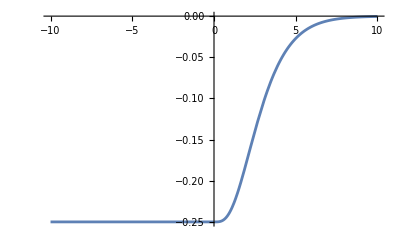

```mathematica
Plot[y[t],{t,-10,10},PlotRange->All]
```